```mathematica
FindTrianglePatternPartitionsAtLevel4[6]
```

{{{1},{2,4},{3,5},{6}},{{1,4},{2},{3,5},{6}},{{1,3},{2,4},{5},{6}},{{1,3},{2,5},{4},{6}},{{1,4},{2,5},{3},{6}}}

```mathematica
EdgesFromPartition[part_]:=Block[{result={}, block={},i,current, combinations,start=Range[5]},
For[i=1,i≤Length[part],i++,
current=part[[i]];
combinations=Subsets[current,{2}];
combinations=Select[combinations,!MemberQ[start,#[[1]]]||!MemberQ[start,#[[2]]]&];
AppendTo[block,Map[#[[1]]<-> #[[2]]&,combinations]]
];
Flatten[Select[block,#≠{}&]]
];
```

```mathematica
With[{part=First[FindTrianglePatternPartitionsAtLevel4[8]]},
part<->EdgesFromPartition[part]
]
```

{{1},{2,4},{3,5},{6,7,8}}<->{6<->7,6<->8,7<->8}

```mathematica
With[{part=Last[FindTrianglePatternPartitionsAtLevel4[8]]},
part<->EdgesFromPartition[part]
]
```

{{1,4,8},{2,5},{3,7},{6}}<->{1<->8,4<->8,3<->7}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[6]}]//Tally//Sort
```

{{0,5}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[7]}]//Tally//Sort
```

{{1,15},{2,20}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[8]}]//Tally//Sort
```

{{2,15},{3,110},{4,30},{5,30}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[9]}]//Tally//Sort
```

{{4,170},{5,340},{6,205},{7,120},{9,40}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[10]}]//Tally//Sort
```

{{6,850},{7,775},{8,1550},{10,480},{11,200},{14,50}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[11]}]//Tally//Sort
```

{{8,2100},{9,4375},{10,3150},{11,2805},{12,2960},{14,600},{15,485},{16,300},{20,60}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[12]}]//Tally//Sort
```

{{10,2100},{11,18200},{12,6475},{13,18900},{14,6860},{15,9310},{16,1190},{17,5040},{18,700},{19,1050},{21,670},{22,420},{27,70}}

```mathematica
Table[Length[EdgesFromPartition[p]],{p,FindTrianglePatternPartitionsAtLevel4[13]}]//Tally//Sort
```

$Aborted

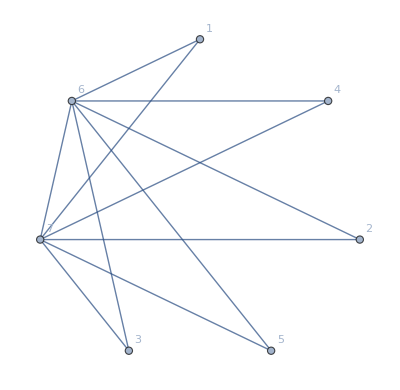

```mathematica
Graph[DeleteDuplicates[Flatten[Table[EdgesFromPartition[p],{p,FindTrianglePatternPartitionsAtLevel4[7]}]]], GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```

```mathematica
Select[FindTrianglePatternPartitionsAtLevel4[8],EdgesFromPartition[#]=={}&]
```

{}

```mathematica
Monitor[Table[
Length[FindTrianglePatternPartitionsAtLevel4[k]],
{k,6,12}],k]
```

{5,35,185,875,3905,16835,70985}

```mathematica
{5,35,185,875,3905,16835,70985}/5
```

{1,7,37,175,781,3367,14197}

```mathematica
Table[n->5(4^(n-5)-3^(n-5)),{n,0,10}]
```

{0→-3905/248832,1→-875/20736,2→-185/1728,3→-35/144,4→-5/12,5→0,6→5,7→35,8→185,9→875,10→3905}

```mathematica
Monitor[Table[
Map[First[EdgesFromPartition[#]]&,FindTrianglePatternPartitionsAtLevel4[k]]//DeleteDuplicates//Length,
{k,6,12}],k]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{1,11,16,21,26,31,36}

```mathematica
Monitor[Table[
Map[First[EdgesFromPartition[#]]&,FindTrianglePatternPartitionsAtLevel4[k]]//DeleteDuplicates//Length,
{k,13,13}],k]
```

{41}

```mathematica
Monitor[Table[
Map[First[EdgesFromPartition[#]]&,FindTrianglePatternPartitionsAtLevel4[k]]//DeleteDuplicates//Length,
{k,14,14}],k]
```

{46}

```mathematica
Table[(3n-6)-10,{n,5,20}]
```

{-1,2,5,8,11,14,17,20,23,26,29,32,35,38,41,44}

```mathematica
Monitor[Table[
Length[FindTrianglePatternPartitionsAtLevel4[k]],
{k,6,12}],k]
```

{5,35,185,875,3905,16835,70985}

```mathematica
Monitor[Table[
Length[FindTrianglePatternPartitionsAtLevel4[k]]/5,
{k,5,12}],k]
```

{0,1,7,37,175,781,3367,14197}

```mathematica
Monitor[Table[
Length[FindTrianglePatternPartitionsAtLevel4[k]]/5,
{k,5,13}],k]
```

{0,1,7,37,175,781,3367,14197,58975}

```mathematica
Table[4^n-3^n,{n,0,15}]
```

{0,1,7,37,175,781,3367,14197,58975,242461,989527,4017157,16245775,65514541,263652487,1059392917}

```mathematica
FullSimplify[4^n-3^n]
```

-3^n+4^n

```mathematica
nmax=12;t[n_,k_]:=1/(k-3)!*Sum[(-1)^(k-j-1)*Binomial[k-3,j]*(j+3)^(n-3),{j,0,k-3}];TableForm[Table[t[n,k],{n,3,nmax},{k,3,n}]]
```

1 |  |  |  |  |  |  |  |  | 
3 | 1 |  |  |  |  |  |  |  | 
9 | 7 | 1 |  |  |  |  |  |  | 
27 | 37 | 12 | 1 |  |  |  |  |  | 
81 | 175 | 97 | 18 | 1 |  |  |  |  | 
243 | 781 | 660 | 205 | 25 | 1 |  |  |  | 
729 | 3367 | 4081 | 1890 | 380 | 33 | 1 |  |  | 
2187 | 14197 | 23772 | 15421 | 4550 | 644 | 42 | 1 |  | 
6561 | 58975 | 133057 | 116298 | 47271 | 9702 | 1022 | 52 | 1 | 
19683 | 242461 | 724260 | 830845 | 447195 | 124887 | 18900 | 1542 | 63 | 1

```mathematica
Table[t[n,4],{n,3,15}]
```

{0,1,7,37,175,781,3367,14197,58975,242461,989527,4017157,16245775}

```mathematica
t[n,3]
```

3^(-3+n)

```mathematica
Simplify[t[n,4]]
```

-3^(-3+n)+4^(-3+n)

```mathematica
Differences[Table[t[n,4],{n,3,15}]]
```

{1,6,30,138,606,2586,10830,44778,183486,747066,3027630,12228618}

## Now looking which edge destroys most solutions

```mathematica
FindTrianglePatternPartitionsAtLevel4[7]
```

{{{1},{2,4},{3,5},{6,7}},{{1},{2,4},{3,5,6},{7}},{{1},{2,4},{3,5,7},{6}},{{1},{2,4,6},{3,5},{7}},{{1},{2,4,7},{3,5},{6}},{{1,4},{2},{3,5},{6,7}},{{1,4},{2},{3,5,6},{7}},{{1,4},{2},{3,5,7},{6}},{{1,4,6},{2},{3,5},{7}},{{1,4,7},{2},{3,5},{6}},{{1,3},{2,4},{5},{6,7}},{{1,3},{2,5},{4},{6,7}},{{1,4},{2,5},{3},{6,7}},{{1,3},{2,4},{5,6},{7}},{{1,3},{2,5,6},{4},{7}},{{1,4},{2,5,6},{3},{7}},{{1,3},{2,4},{5,7},{6}},{{1,3},{2,5,7},{4},{6}},{{1,4},{2,5,7},{3},{6}},{{1,3},{2,4,6},{5},{7}},{{1,3},{2,5},{4,6},{7}},{{1,4,6},{2,5},{3},{7}},{{1,3},{2,4,7},{5},{6}},{{1,3},{2,5},{4,7},{6}},{{1,4,7},{2,5},{3},{6}},{{1,6},{2,4},{3,5},{7}},{{1,7},{2,4},{3,5},{6}},{{1,4},{2,6},{3,5},{7}},{{1,4},{2,7},{3,5},{6}},{{1,3,6},{2,4},{5},{7}},{{1,3,6},{2,5},{4},{7}},{{1,4},{2,5},{3,6},{7}},{{1,3,7},{2,4},{5},{6}},{{1,3,7},{2,5},{4},{6}},{{1,4},{2,5},{3,7},{6}}}

```mathematica
EdgesFromPartition[{{1},{2,4},{3,5},{6,7}}]
```

{6<->7}

```mathematica
EdgeToPartition[n_]:=Block[{triangles = FindTrianglePatternPartitionsAtLevel4[n], result=Association[],edges},
Table[
edges=EdgesFromPartition[p];
Table[
If[!KeyExistsQ[result,e],result[e]={}];
result[e]=Append[result[e],p]
,
{e,edges}]
,{p,triangles}
];
result
]
```

```mathematica
EdgeToPartition2[triangles_]:=Block[{ result=Association[],edges},
Table[
edges=EdgesFromPartition[p];
Table[
If[!KeyExistsQ[result,e],result[e]={}];
result[e]=Append[result[e],p]
,
{e,edges}]
,{p,triangles}
];
result
]
```

```mathematica
TableForm[Table[
With[{assoc=EdgeToPartition[size]},
{size,Length[Keys[assoc]],Length[assoc[First[Keys[assoc]]]]}
],
{size,6,10}
]
]
```

First::nofirst: {} has zero length and no first element.

6 | 0 | 2
7 | 11 | 5
8 | 18 | 35
9 | 26 | 185
10 | 35 | 875

```mathematica
TableForm[Table[
With[{assoc=EdgeToPartition[size]},
{size,Length[Keys[assoc]],Map[SetsToSymbol2,assoc[First[Keys[assoc]]]]}
],
{size,7,8}
], TableDepth->1
]
```

{7,11,{v1x24x35x67,v14x2x35x67,v13x24x5x67,v13x25x4x67,v14x25x3x67}}
{8,18,{v1x24x35x678,v1x24x3567x8,v1x24x358x67,v1x2467x35x8,v1x248x35x67,v14x2x35x678,v14x2x3567x8,v14x2x358x67,v1467x2x35x8,v148x2x35x67,v13x24x5x678,v13x25x4x678,v14x25x3x678,v13x24x567x8,v13x2567x4x8,v14x2567x3x8,v13x24x58x67,v13x258x4x67,v14x258x3x67,v13x2467x5x8,v13x25x467x8,v1467x25x3x8,v13x248x5x67,v13x25x48x67,v148x25x3x67,v167x24x35x8,v18x24x35x67,v14x267x35x8,v14x28x35x67,v1367x24x5x8,v1367x25x4x8,v14x25x367x8,v138x24x5x67,v138x25x4x67,v14x25x38x67}}

```mathematica
Table[5(4^n-3^n),{n,0,10}]
```

{0,5,35,185,875,3905,16835,70985,294875,1212305,4947635}

## Now let's see how many we need to destroy them all.

To do this we just test for each edge combination how many we can get

```mathematica
ChooseSome[set_,size_]:=If[Length [set]<size,set,RandomSample[set,size]]
```

```mathematica
FindEdgesThatDestroyAll[n_]:=Block[{
trianglePartitions,
edgeAssoc,
edges,
size, 
covered,
subsets,pos,min,max, coverLength
},
trianglePartitions=FindTrianglePatternPartitionsAtLevel4[n];
edgeAssoc = EdgeToPartition2[trianglePartitions];
Print["number of nodes ", n," triangle partitions : ", Length[trianglePartitions]];
edges=Keys[edgeAssoc];
Print[edges];
Monitor[
For[size=2, size≤Length[edges], size++,
min=100000000000000000000;
max=-100000000000000000000;
Print["size : ", size, " of ",Length[edges]];
subsets=Subsets[edges,{size}];
pos=1;
Table[
pos++;
covered = DeleteDuplicates[Flatten[Table [edgeAssoc[e],{e,edgeTrial}],1]];
coverLength=Length[covered];
min=Min[min,coverLength];
max=Max[max,coverLength];
If[coverLength==Length[trianglePartitions],
With[{g=Graph[Range[n],Join[{1<->2,2<->3,3<->4,4<->5,5<->1},edgeTrial]]},
If[ ConnectedGraphQ[g]&& Length[First[FindClique[g]]]<5,
Print[edgeTrial, "   ",Length[covered], "  " , PlanarGraphQ[Graph[covered]], "    ", 
{Labeled[
Graph[g,GraphHighlight->First[FindClique[g]],GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->300],
{EdgeCount[g],3*VertexCount[g]-6}],FindClique[g]}
];
Break[]
]
];
;
];
,{edgeTrial,subsets}
];
Print["    min ", min, ", max ",max];
],
{size,pos,Length[subsets],Length[covered]}
];

]
```

number of nodes 7 triangle partitions : 35

{6<->7,3<->6,5<->6,3<->7,5<->7,2<->6,4<->6,2<->7,4<->7,1<->6,1<->7}

size : 2 of 11

min 8, max 10

size : 3 of 11

min 11, max 15

size : 4 of 11

min 14, max 20

size : 5 of 11

min 15, max 25

size : 6 of 11

min 20, max 28

size : 7 of 11

min 23, max 31

size : 8 of 11

min 26, max 32

size : 9 of 11

min 29, max 33

size : 10 of 11

min 30, max 34

size : 11 of 11

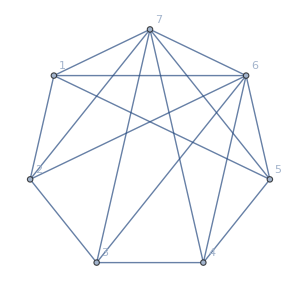
{6<->7,3<->6,5<->6,3<->7,5<->7,2<->6,4<->6,2<->7,4<->7,1<->6,1<->7}   35  False    {-Graphics-{16,15},{{1,2,6,7}}}

```mathematica
FindEdgesThatDestroyAll[7]
```

number of nodes 8 triangle partitions : 185

{6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,5<->8,2<->6,4<->6,2<->7,2<->8,4<->7,4<->8,1<->6,1<->7,1<->8}

size : 2 of 18

min 56, max 70

size : 3 of 18

min 77, max 95

size : 4 of 18

min 98, max 120

size : 5 of 18

min 105, max 145

size : 6 of 18

min 125, max 157

size : 7 of 18

min 137, max 169

size : 8 of 18

min 149, max 175

size : 9 of 18

min 155, max 185

size : 10 of 18

min 162, max 185

size : 11 of 18

min 168, max 185

size : 12 of 18

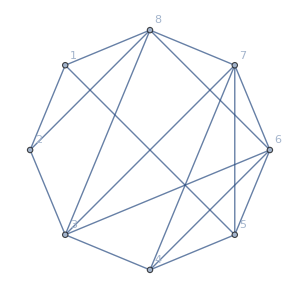
{6<->7,6<->8,7<->8,3<->6,5<->6,3<->7,3<->8,5<->7,4<->6,2<->8,4<->7,1<->8}   185  False    {-Graphics-{17,18},{{3,4,6,7}}}

```mathematica
FindEdgesThatDestroyAll[8]
```

number of nodes 9 triangle partitions : 875

{6<->7,6<->8,6<->9,7<->8,7<->9,8<->9,3<->6,5<->6,3<->7,3<->8,3<->9,5<->7,5<->8,5<->9,2<->6,4<->6,2<->7,2<->8,2<->9,4<->7,4<->8,4<->9,1<->6,1<->7,1<->8,1<->9}

size : 2 of 26

min 296, max 370

size : 3 of 26

min 407, max 485

size : 4 of 26

min 494, max 600

size : 5 of 26

min 555, max 715

size : 6 of 26

min 620, max 763

size : 7 of 26

min 679, max 811

size : 8 of 26

min 700, max 835

size : 9 of 26

min 745, max 875

size : 10 of 26

min 762, max 875

size : 11 of 26

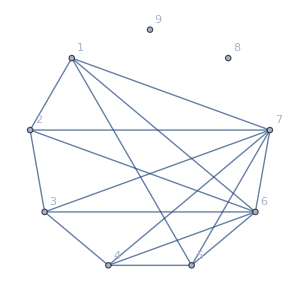
{6<->7,3<->6,5<->6,3<->7,5<->7,2<->6,4<->6,2<->7,4<->7,1<->6,1<->7}   875  False    {-Graphics-{16,21},{{1,2,6,7}}}

```mathematica
FindEdgesThatDestroyAll[9]
```

```mathematica
FindEdgesThatDestroyAll[10]
```

number of nodes 10 triangle partitions : 3905

{6<->7,6<->8,6<->9,6<->10,7<->8,7<->9,7<->10,8<->9,8<->10,9<->10,3<->6,5<->6,3<->7,3<->8,3<->9,3<->10,5<->7,5<->8,5<->9,5<->10,2<->6,4<->6,2<->7,2<->8,2<->9,2<->10,4<->7,4<->8,4<->9,4<->10,1<->6,1<->7,1<->8,1<->9,1<->10}

size : 2 of 35

min 1400, max 1750

size : 3 of 35

min 1925, max 2275

size : 4 of 35

min 2282, max 2760

size : 5 of 35

min 2625, max 3265

size : 6 of 35

min 2828, max 3457

size : 7 of 35

min 3073, max 3649

size : 8 of 35

$Aborted

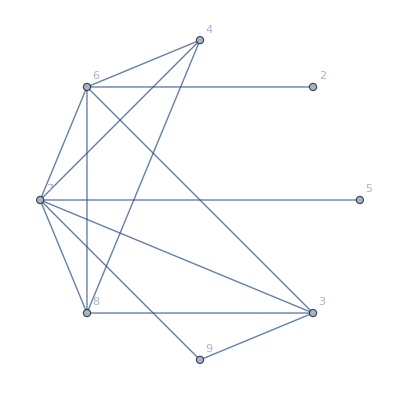

```mathematica
Graph[{6<->7,6<->8,7<->8,7<->9,3<->6,3<->7,3<->8,3<->9,5<->7,2<->6,4<->6,4<->7,4<->8}, GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```